## Import data files and create interpolation objects

Form factors  span the range q = 1 to 2000 keV and E = 1 eV to 2 keV. 
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].
Data is optimised for q = 1 to 500 keV and E = 1 eV to 1 keV. 
Interpolation outside this range is not accurate.

```mathematica
SetDirectory[NotebookDirectory[]];
LHe1sgrid=Import["He_1s_grid.dat"];
ResetDirectory[];

fHe1s=Interpolation[LHe1sgrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

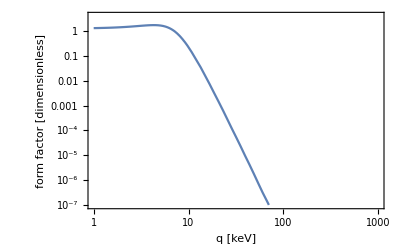

```mathematica
EtestkeV=0.03;

LogLogPlot[{fHe1s[q,EtestkeV]},{q,1,200},PlotRange->{{1,1000},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"}]
```

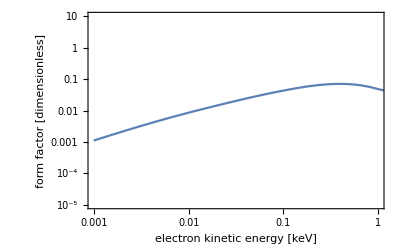

```mathematica
qtestkeV=10;

LogLogPlot[{fNe1s[qtestkeV,E1]},{E1,0.001,1000},PlotRange->{{0.001,1},{10^-5,10}},Frame->True,FrameLabel->{"electron kinetic energy [keV]","form factor [dimensionless]"}]
```